```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
doubleSlitVisibilities ={{12.5,0.0622182894158},{18.75,0.262046530327},{25.0,0.413845613926},{31.25,0.520890621022},{37.5,0.60422967464},{50.0,0.678435518874},{75.0,0.741292072381},{100.0,0.785590343359},{125.0,0.780171812745},{150.0,0.767152768553},{175.0,0.802659199759},{200.0,0.797133521121}}




doubleSlitVisibilitiesEbar = {{{12.5,0.0622182894158},ErrorBar[0.0800204779167]},{{18.75,0.262046530327},ErrorBar[0.065750275784]},{{25.0,0.413845613926},ErrorBar[0.105969599251]},{{31.25,0.520890621022},ErrorBar[0.0446732860123]},{{37.5,0.60422967464},ErrorBar[0.0987438260883]},{{50.0,0.678435518874},ErrorBar[0.046147922361]},{{75.0,0.741292072381},ErrorBar[0.0603877930997]},{{100.0,0.785590343359},ErrorBar[0.0441566188039]},{{125.0,0.780171812745},ErrorBar[0.0565851294361]},{{150.0,0.767152768553},ErrorBar[0.0456716713411]},{{175.0,0.802659199759},ErrorBar[0.0461395887709]},{{200.0,0.797133521121},ErrorBar[0.0417061851672]}}
```

{{12.5,0.0622183},{18.75,0.262047},{25.,0.413846},{31.25,0.520891},{37.5,0.60423},{50.,0.678436},{75.,0.741292},{100.,0.78559},{125.,0.780172},{150.,0.767153},{175.,0.802659},{200.,0.797134}}

{{{12.5,0.0622183},ErrorBar[0.0800205]},{{18.75,0.262047},ErrorBar[0.0657503]},{{25.,0.413846},ErrorBar[0.10597]},{{31.25,0.520891},ErrorBar[0.0446733]},{{37.5,0.60423},ErrorBar[0.0987438]},{{50.,0.678436},ErrorBar[0.0461479]},{{75.,0.741292},ErrorBar[0.0603878]},{{100.,0.78559},ErrorBar[0.0441566]},{{125.,0.780172},ErrorBar[0.0565851]},{{150.,0.767153},ErrorBar[0.0456717]},{{175.,0.802659},ErrorBar[0.0461396]},{{200.,0.797134},ErrorBar[0.0417062]}}

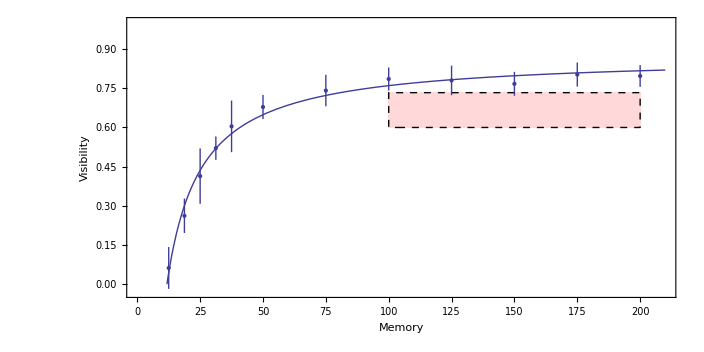

```mathematica
Show[RegionPlot[True,{x,100,200},{y,0.6,0.7333},BoundaryStyle->Dashed, PlotStyle->LightRed,Frame->True,PlotRange->{{0,210},{-0.03,1}}, AspectRatio->0.5,BaseStyle->{FontFamily->"Times",FontSize->24}, FrameLabel->{"Memory","Visibility"}],Plot[-0.8748092117706676(6.64970293062812-(x-5.140798425162953))/(6.64970293062812+(x-5.140798425162953)),{x,5,210},PlotRange->{{0,210},{-0,1}}],ErrorListPlot[doubleSlitVisibilitiesEbar]]
```

```mathematica
VDUUB = AAAA ((MMM-III)-DDD)/((MMM-III)+DDD)
```

(AAAA (-DDD-III+MMM))/(DDD-III+MMM)

```mathematica
FindFit[doubleSlitVisibilities,VDUUB,{AAAA,III,DDD},MMM]
```

{AAAA→0.874809,III→5.1408,DDD→6.6497}

```mathematica
nlm = NonlinearModelFit[doubleSlitVisibilities,VDUUB,{AAAA,III,DDD},MMM]
```

FittedModel[(0.874809 (-«19»+MMM))/(1.5089+MMM)]

```mathematica
{params,confidenceInt,res}=nlm[{"BestFitParameters","ParameterConfidenceIntervals","FitResiduals"}]
```

{{AAAA→0.874809,III→5.1408,DDD→6.6497},{{0.834837,0.914782},{2.88675,7.39485},{5.1163,8.18311}},{0.0179125,-0.0384748,-0.0220755,0.00123501,0.0276714,0.0294988,0.0185494,0.0253961,-0.00267199,-0.030866,-0.00623581,-0.0199391}}

```mathematica
resnorm=Total[res^2]
```

0.00631125

```mathematica
confidenceInt
```

{{0.834837,0.914782},{2.88675,7.39485},{5.1163,8.18311}}

```mathematica
-(0.8348368097578801-0.9147816137834551)/2
```

0.0399724

```mathematica
-(2.8867465906757546-7.394850259650152)/2
```

2.25405

```mathematica
-(5.116300012839759-8.18310584841648)/2
```

1.5334